# Thermodynamics

## Statistical Physics of Particles by Kardar: Computations and Visualizations

## 1.4 The Second Law

## 1.5 Carnot Engines

A Carnot Engine is any engine that is reversible, runs in a cycle, with all of its heat exchanges taking place at a source temperature , and a sing temperature . A reversible process is one that can be run backward in time by simply reversing its inputs and outputs. It is the thermodynamic equivalence of frictionless motion in mechanics.

Since time reversibility implies equilibrium, a reversible transformation must be quasi-static, but reverse is not necessarily true.

The distinguishing characteristic of the Carnot engine is that heat exchanges with the surroundings are carried out only at two temperatures. The zeroth law allow us to select two isotherms at temperatures  and  for these heat exchanges. To complete the Carnot cycle we have to connect these isotherms by reversible adiabatic paths in the coordinate space.

Since heat is not a function of state, we don’t know how to construct such paths in general. Fortunately, we have sufficient information at this point to construct a Carnot engine using an ideal gas as its internal working substance. Let us compute the adiabatic curves for a monoatomic ideal gas with an internal energy:

```mathematica
EnergyPressureVolumeIdealGas[P_,V_]:= 3/2 P V
```

Thus we can differentiate:

```mathematica
(* Making a function for total differentials *)
d[f_,vars_List]:=Total[D[f,#] Dt[#]&/@vars]
```

```mathematica
dQ = d[EnergyPressureVolumeIdealGas[P,V],{V,P}] + P DifferentialD[V]//Expand
```

P ⅆV+3/2 V Dt[P]+3/2 P Dt[V]

Now in an adiabatic condition  is zero thus:

```mathematica
dQ ==0
```

P ⅆV+3/2 V Dt[P]+3/2 P Dt[V]==0

```mathematica
2 dQ ==0//Expand
```

2 P ⅆV+3 V Dt[P]+3 P Dt[V]==0

Solving this (Mathematica is being a total ass) would result:

```mathematica
P[V_, γ_,constant_] := constant/V^γ
```

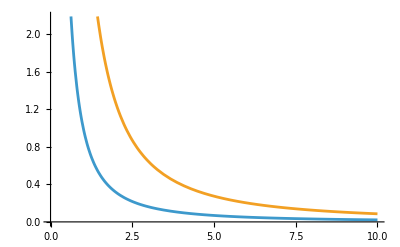

```mathematica
Plot[{
P[V,5/3,1],
P[V,5/3, 4]
},{V,0,10}]
```

This and the two isothermal processes for  and . We would get:

```mathematica
IsoThermPressure[V_,constant_]:=(constant/V)
```

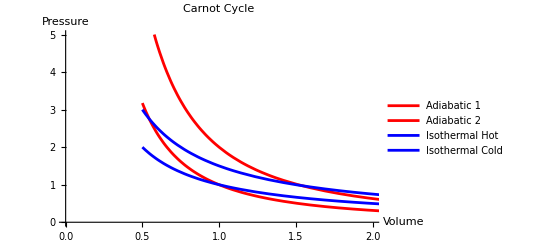

```mathematica
Plot[{P[V,5/3,1],P[V,5/3,2],IsoThermPressure[V,1],IsoThermPressure[V,1.5]},{V,0.5,5},PlotRange->{{0,2},{0,5}},PlotStyle->{Red,Red,Blue,Blue},PlotLegends->{"Adiabatic 1","Adiabatic 2","Isothermal Hot","Isothermal Cold"},AxesLabel->{"Volume","Pressure"},PlotLabel->"Carnot Cycle"]
```

The adiabatic curves are clearly distinct from the isotherms, and we can select two such curves to intersect our isotherms, thereby completing a Carnot cycle . The assumption of  is not necessary. In fact, a similar construction is possible for any two - parameter system with .
    
Carnot' s theorem No engine operating between two reservoirs (at temperatures TH and TC) is more efficient than a Carnot engine operating between them.

Since a Carnot engine is reversible, it can be run backward as a refrigerator.

Let us denote the heat exchanges of the non - Carnot and Carnot engines by , , and , respectively . The net effect of the two engines is to transfer heat equal to  C from  to  .

According to Clausius' s statement, the quantity of transferred heat cannot be negative, that is,

```mathematica
QH >= Subscript[QC, carnot]
```

QH≥QC_carnot

Since the same quantity of work  is involved in this process, we conclude that:

```mathematica
η[W_,Q_]:=W/Q;
η[W,Subscript[Q, nonCarnot]]<= η[W,Subscript[Q, Carnot]]
```

W/Q_nonCarnot≤W/Q_Carnot

Corollary All reversible (Carnot) engines have the same universal efficiency , since each can be used to run any other one backward .

The thermodynamic temperature scale : as shown earlier, it is at least theoretically possible to construct a Carnot engine using an ideal gas (or any other two - parameter system) as working substance .

Independent of the material used, and design and construction, all such cyclic and reversible engines have the same maximum theoretical efficiency.

Since this maximum efficiency is only dependent on two temperatures, it can be used to construct a temperature scale. Such a temperature scale has the attractive property of being independent of the properties of any material (e.g., the ideal gas).

Consider two Carnot engines running in series, one between temperatures  and the other between  (). Denote the heat exchanges and work outputs, of the two engines by  and , respectively. Note that the heat dumped by the first engine is taken in by the second, so the combined effect is another Carnot engine (since each component is reversible) with heat exchanges  and work output .

```mathematica
Clear[η];
```

Using the universal efficiency, the three heat exchanges are related by:

```mathematica
heatRelations = {
Q2 ==Q1(1-η[T1,T2]),
Q3 == Q2 (1-η[T2,T3]),
Q3 ==Q1(1-η[T1,T3])
}
```

Comparison of the final two expressions yields:

```mathematica
heatRelations[[2]][[2]] ==heatRelations[[3]][[2]]/.Q2->heatRelations[[1]][[2]]
```

Q1 (1-η[T1,T2]) (1-η[T2,T3])==Q1 (1-η[T1,T3])

```mathematica
/.Q1->1
```

(1-η[T1,T2]) (1-η[T2,T3])==1-η[T1,T3]

This property implies that  can be written as a ration of the form , which by convention is set to , that is,

```mathematica
η[T1_,T2_]:=1-T2/T1
```

This equation defines temperature up to a constant of proportionality, which is again set by choosing the triple point of water, ice, and steam. So far we’ve been using  and  interchangeably. In fact, by running a Carnot cycle for a perfect gas, it can be proved that the ideal gas and thermodynamic temperature scales are equivalent.

All thermodynamic temperatures are positive, since according to equation of , the heat extracted from a temperature  is proportional to it. If a negative temperature existed, an engine operating between it and a positive temperature would extract heat from both reservoirs and convert the sum total to work, in violation of Kelvin’s statement of the second law.

## 1.6 Entropy